Evaluating the CAPM and Comparing to Market Data

```mathematica
(*Import Market Returns*)
MarketReturns=Import["/Users/nickchristo/Downloads/Fall 2024/AMS 511/Workshop/vnMarketReturns.m"];
(*Import Asset Returns (30 Assets)*)
AssetReturns=Import["/Users/nickchristo/Downloads/Fall 2024/AMS 511/Workshop/mnReturns.m"];
(*Import the Market Caps of the Assets*)
MarketCaps=Import["/Users/nickchristo/Downloads/Fall 2024/AMS 511/Workshop/vnMarketCaps.m"];
```

```mathematica
(*Fit the CAPM for each asset using linear regression*)

(*Assume Risk-Free Rate of 1.5%, for simplicity*)
rDaily=(1+0.015)^(1/250)-1;(*Find daily risk-free rate*)
```

```mathematica
(*Find excess return for the market and assets for each day it is recorded*)
MarketExcessReturn=MarketReturns-rDaily;
AssetExcessReturns=AssetReturns-rDaily;
```

```mathematica
(*Use LinearModelFit[] for each asset to find betas and error var.*)
AssetModels={};
Table[AssetModels=Append[AssetModels, LinearModelFit[Transpose[{MarketExcessReturn, AssetExcessReturns[[All, y]]}], {x}, x, IncludeConstantBasis->False]], {y,1,30}];
```

```mathematica
(*Extract the Betas from each model and place them in a vector*)
Betas = Table[AssetModels[[x]]["BestFitParameters"][[1]], {x, 1, 30}];

(*Repeat for estimated error variances*)
ErrorVars = Table[AssetModels[[x]]["EstimatedVariance"], {x,1,30}];

(*Table view of Beta and Error Var. corresponding to each Asset.*)
TableForm[Transpose[{Table[x, {x,1,30}],Betas, ErrorVars}], TableHeadings->{None, {"Asset","Beta","Error Var"}}]
```

Asset | Beta | Error Var
1 | 1.10034 | 0.0000468738
2 | 1.11642 | 0.0000939173
3 | 1.02282 | 0.000175483
4 | 1.35401 | 0.000108335
5 | 1.39659 | 0.000127316
6 | 1.14319 | 0.000100392
7 | 1.16158 | 0.000113601
8 | 0.647717 | 0.0000569055
9 | 1.04638 | 0.0000808828
10 | 1.34619 | 0.000133024
11 | 1.01903 | 0.0000710069
12 | 1.46889 | 0.0000822754
13 | 1.02938 | 0.0000751994
14 | 1.21489 | 0.000147971
15 | 1.06746 | 0.0000923272
16 | 0.855936 | 0.0000487559
17 | 1.37291 | 0.0000705654
18 | 0.742885 | 0.0000712136
19 | 0.897792 | 0.000104764
20 | 1.24698 | 0.000131645
21 | 1.04095 | 0.000146248
22 | 0.894732 | 0.0000768373
23 | 0.686703 | 0.0000650705
24 | 0.94094 | 0.0000539514
25 | 1.06364 | 0.00010559
26 | 1.08837 | 0.0000550174
27 | 0.717201 | 0.0000880127
28 | 1.24661 | 0.0000898196
29 | 0.989723 | 0.000184624
30 | 0.712694 | 0.000106074

```mathematica
(*Use estimates of Betas and Error Vars. to compute allocations of each stock under CAPM*)

(*Find efficient allocations and normalize so the allocations sum to 1*)
EfficientPortfolio=#/Total[#]&[Betas/ErrorVars];

(*Ensure asset allocation sums to 1.*)
Total[EfficientPortfolio]
```

1.

```mathematica
(*Show the efficient allocation by asset.*)
TableForm[Table[{x, EfficientPortfolio[[x]](100)}, {x, 1, 30}], TableHeadings->{None, {"Asset", "Allocation(%)"}}]
```

Asset | Allocation(%)
1 | 6.4743
2 | 3.27852
3 | 1.60754
4 | 3.44707
5 | 3.02542
6 | 3.14064
7 | 2.82011
8 | 3.13927
9 | 3.56805
10 | 2.79109
11 | 3.95809
12 | 4.92397
13 | 3.77538
14 | 2.26441
15 | 3.18875
16 | 4.84185
17 | 5.36595
18 | 2.87711
19 | 2.36354
20 | 2.61248
21 | 1.96309
22 | 3.21157
23 | 2.91059
24 | 4.81013
25 | 2.77822
26 | 5.45598
27 | 2.24746
28 | 3.82786
29 | 1.47851
30 | 1.85307

```mathematica
(*Use actual market caps. to find actual market allocations*)

(*Actual proportion is the market cap. over the summed market caps.*)
MarketCapProportions=#/Total[#]&[MarketCaps];

(*Show a table of the actual market capatalization in percentages*)
TableForm[Table[{x,MarketCapProportions[[x]](100)}, {x,1,30}], TableHeadings->{None, {"Asset", "Market Cap. (%)"}}]
```

Asset | Market Cap. (%)
1 | 0.944307
2 | 1.27637
3 | 1.12203
4 | 21.7805
5 | 1.22359
6 | 0.982697
7 | 1.86365
8 | 2.14815
9 | 2.11399
10 | 2.95421
11 | 0.403528
12 | 1.1832
13 | 3.2155
14 | 1.37521
15 | 1.18656
16 | 2.01832
17 | 3.90191
18 | 4.61292
19 | 1.67573
20 | 1.90327
21 | 20.0673
22 | 2.15041
23 | 3.13074
24 | 2.48911
25 | 0.351252
26 | 3.41786
27 | 2.07649
28 | 4.52735
29 | 0.373916
30 | 3.52994

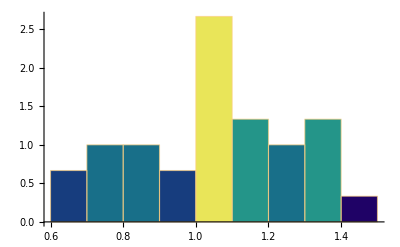

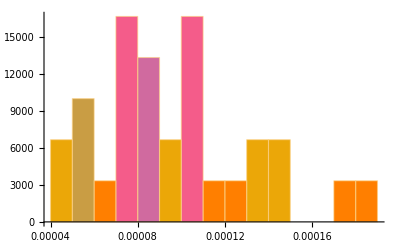

```mathematica
(*Create Histograms of Betas and Error variances to visualize the distributions*)
Histogram[Betas,{0.10}, "PDF", ColorFunction->"BlueGreenYellow", PlotRange->All]
Histogram[ErrorVars, {0.00001}, "PDF", ColorFunction->"FruitPunchColors", PlotRange->All]
```

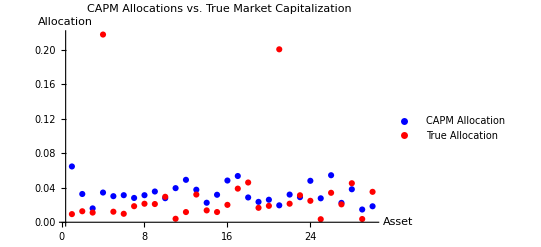

```mathematica
(*Plot true market allocation for each asset against theoretical efficient allocation under CAPM*)
ListPlot[{EfficientPortfolio, MarketCapProportions}, PlotRange->All, PlotLabel->"CAPM Allocations vs. True Market Capitalization", PlotLegends->{"CAPM Allocation", "True Allocation"}, PlotStyle->{Blue, Red}, AxesLabel->{"Asset", "Allocation"}, LabelStyle->{Black,10}]
```

It seems that for more than half of the assets the theoretical efficient allocation given by the CAPM is slightly larger than the true allocation that is given in the data. There are two assets, specifically assets 4 and 21 where the true allocation is greater than the theoretical efficient allocation by 18.33% and 18.10%, respectively. If you consider that the true market capitalization of these two assets alone is above 40%, then it is clear to see why the true allocation is lower than the theoretical efficient allocation in most of the other assets. If the market capitalization of these assets decreased to a level closer to their respective theoretical allocation, and the excess capital invested in these assets were dispersed evenly among the other 28 assets, then the theoretical CAPM allocation and the true allocation would be closer. Some other large discrepancies are asset 12, where the CAPM allocation is about 3.7% higher than the true allocation, and asset 1, where the CAPM allocation is about 5.5% higher than the true allocation.